```mathematica
ClearAll["Global`*"]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/data.csv"][[2;;]];
t=Table[{t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

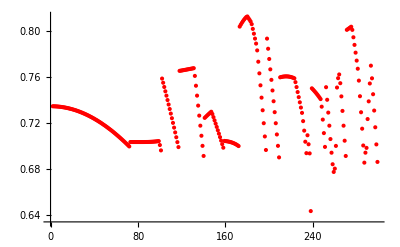

```mathematica
plot1=ListPlot[t,PlotStyle->Red,PlotRange->Full]
```